```mathematica
lst1= List[];
lst1=Import["C:/Users/Артем/Desktop/polynom points1.txt","Table"];
lst2= List[];
lst2=Import["C:/Users/Артем/Desktop/polynom points2.txt","Table"];
lst3= List[];
lst3=Import["C:/Users/Артем/Desktop/polynom points3.txt","Table"];
lst4= List[];
lst4=Import["C:/Users/Артем/Desktop/polynom points4.txt","Table"];
lst5= List[];
lst5=Import["C:/Users/Артем/Desktop/polynom points5.txt","Table"];
```

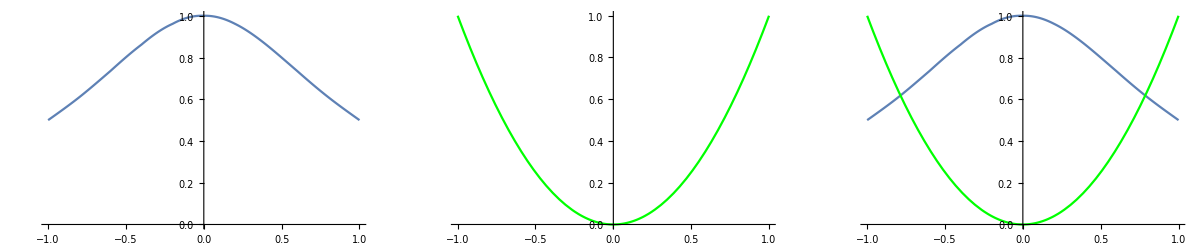

```mathematica
GraphicsRow[{ListLinePlot[lst1],Plot[x^2, {x, -1,1}, PlotStyle->Green],Show[ListLinePlot[lst1],Plot[x^2, {x, -1,1}, PlotStyle->Green]]}]
```

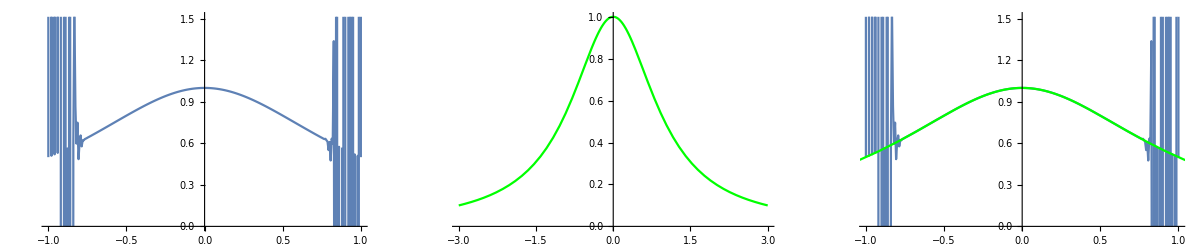

```mathematica
GraphicsRow[{ListLinePlot[lst2],Plot[1/(1+x^2), {x, -3,3}, PlotStyle->Green],Show[ListLinePlot[lst2],Plot[1/(1+x^2), {x, -3,3}, PlotStyle->Green]]}]
```

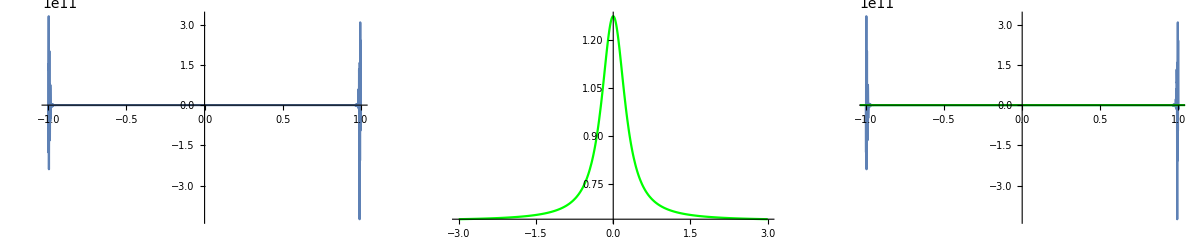

```mathematica
GraphicsRow[{ListLinePlot[lst3, PlotRange->All],Plot[1/ArcTan[1+10*x*x], {x, -3,3}, PlotStyle->Green,PlotRange->All],Show[ListLinePlot[lst3, PlotRange->All],Plot[1/ArcTan[1+10*x*x], {x, -3,3}, PlotStyle->Green,PlotRange->All]]}]
```

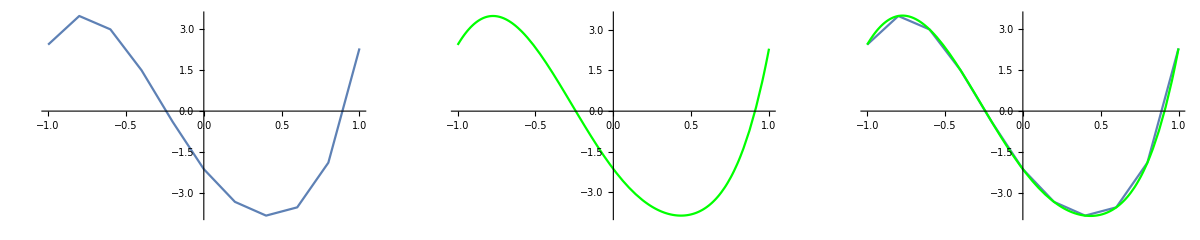

```mathematica
GraphicsRow[{ListLinePlot[lst4, PlotRange->All],Plot[(4x^3+2x^2-4x+2)^(Sqrt[2])+ArcSin[1/(5+x-x^2)]-5, {x, -1,1}, PlotStyle->Green,PlotRange->All],Show[ListLinePlot[lst4, PlotRange->All],Plot[(4x^3+2x^2-4x+2)^(Sqrt[2])+ArcSin[1/(5+x-x^2)]-5, {x, -1,1}, PlotStyle->Green,PlotRange->All]]}]
```

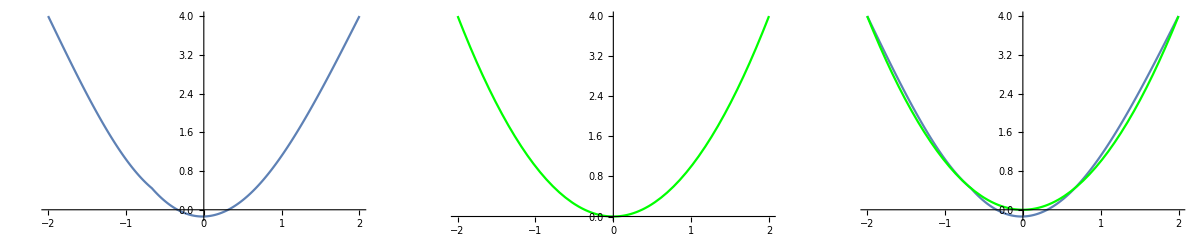

```mathematica
GraphicsRow[{ListLinePlot[lst5],Plot[x*x, {x, -2,2}, PlotStyle->Green],Show[ListLinePlot[lst5],Plot[x*x, {x, -2,2}, PlotStyle->Green]]}]
```